## Imports and helper functions

```mathematica
Needs["QM`"];
Needs["QuantumWalks`"];
Needs["utilities`"];
Needs["GeneralUtilities`"];
Needs["MaTeX`"];

Get[FileNameJoin@{NotebookDirectory[],"stabilityAnalysis.m"}];
Get[FileNameJoin@{NotebookDirectory[],"searchCoinParameters.m"}];
```

```mathematica
normalizePhase[expr_?MatrixQ]:=expr Exp[-I Arg@expr⟦1,1⟧]//Chop;
normalizePhase[expr_List]:=expr Exp[-I Arg@expr⟦1⟧]//Chop;
```

```mathematica
ClearAll@monitorMap;
Attributes@monitorMap=HoldAll;
monitorMap[Map[func_,target_]]:=Module[{iter=0},
Monitor[
Map[(iter++;func@#)&,target],
progressBar[100.iter/Length@target]
]
];
```

## Define QW evolution and try some steps

### 2 steps, fixed coin state

```mathematica
dmAfter2Steps=evolveQW[qwInitState[3],2,θ]//QStateToDensityMatrix//allReal;
dmAfter2StepsAndPTrace=dmAfter2Steps//QPartialTrace[#,2]&;
```

```mathematica
parametricPlot3DFromList[amps_List, θ_Symbol: θ] := ParametricPlot3D[
   Evaluate@MapIndexed[
     {First@#2/2, θ, #1} &,
     amps/Total@amps
     ],
   {θ, 0, Pi},
   PlotRange -> All,
   ImageSize -> Large,
   AxesLabel -> {n, θ, "amplitude"},
   Ticks -> {Transpose[{#/2, #}] &@Range@Length@amps, Automatic, Automatic},
   PlotPoints -> 50,
   MaxRecursion -> 4
   ];

ClearAll[parametricPlotFromDM];
parametricPlotFromDM[dm_iQDensityMatrix, par_Symbol: θ] := With[{
   amps = Diagonal[dm[[1]]]
   },
  ParametricPlot3D[
   Evaluate@MapIndexed[
     {First@#2/2, par, #1} &,
     amps/Total@amps
     ],
   {par, 0, 2 Pi},
   PlotRange -> All,
   ImageSize -> Large,
   AxesLabel -> {n, par, "amplitude"},
   Ticks -> {Transpose[{#/2, #}] &@Range@Length@amps, Automatic, Automatic}
   ]
  ]
parametricPlotFromDMNormalizedPositions[dm_iQDensityMatrix, θ_Symbol: θ] := With[{
   amps = Riffle[#, 0] &@Diagonal[dm[[1]]]
   },
  ParametricPlot3D[
   Evaluate@MapIndexed[
     {First@#2/2, θ, #1} &,
     amps/Total@amps
     ],
   {θ, 0, 2 Pi},
   PlotRange -> All,
   ImageSize -> Large,
   AxesLabel -> {n, θ, "amplitude"},
   Ticks -> {Transpose[{#/2, #}] &@Range@Length@amps, Automatic, Automatic}
   ]
  ]
```

```mathematica
Map[parametricPlotFromDM[#,θ]&][
{dmAfter2Steps,dmAfter2StepsAndPTrace}
]//GraphicsRow[#,ImageSize->800]&
```

-Graphics-

what is the density matrix after 2 steps?

```mathematica
dmAfter2Steps//MF
```

( | 1,↑ | 1,↓ | 2,↑ | 2,↓ | 3,↑ | 3,↓
1,↑ | Cos[θ]^4 | 0 | -Cos[θ]^2 Sin[θ]^2 | -Cos[θ]^3 Sin[θ] | 0 | -Cos[θ]^3 Sin[θ]
1,↓ | 0 | 0 | 0 | 0 | 0 | 0
2,↑ | -Cos[θ]^2 Sin[θ]^2 | 0 | Sin[θ]^4 | Cos[θ] Sin[θ]^3 | 0 | Cos[θ] Sin[θ]^3
2,↓ | -Cos[θ]^3 Sin[θ] | 0 | Cos[θ] Sin[θ]^3 | Cos[θ]^2 Sin[θ]^2 | 0 | Cos[θ]^2 Sin[θ]^2
3,↑ | 0 | 0 | 0 | 0 | 0 | 0
3,↓ | -Cos[θ]^3 Sin[θ] | 0 | Cos[θ] Sin[θ]^3 | Cos[θ]^2 Sin[θ]^2 | 0 | Cos[θ]^2 Sin[θ]^2)

2 steps and then partial trace over the coin

```mathematica
dmAfter2StepsAndPTrace//FullSimplify//MF
```

( | 1 | 2 | 3
1 | Cos[θ]^4 | -Cos[θ]^2 Sin[θ]^2 | 0
2 | -Cos[θ]^2 Sin[θ]^2 | Sin[θ]^2 | Cos[θ]^2 Sin[θ]^2
3 | 0 | Cos[θ]^2 Sin[θ]^2 | Cos[θ]^2 Sin[θ]^2)

```mathematica
parametricPlotFromDM[dmAfter2StepsAndPTrace,θ]
```

-Graphics3D-

2 steps, project over unbiases coin state, and then partial trace over coin

```mathematica
Π=KroneckerProduct[IdentityMatrix[3],ConstantArray[1/2,{2,2}]];
dmAfter2StepsAndProjection=Π.dmAfter2Steps.Π;
dmAfter2StepsAndProjectionAndPTrace=dmAfter2StepsAndProjection//QPartialTrace[#,2]&;
```

```mathematica
dmAfter2StepsAndProjectionAndPTrace//FullSimplify//MF
```

( | 1 | 2 | 3
1 | Cos[θ]^4/2 | -1/2 Cos[θ]^2 Sin[θ] (Cos[θ]+Sin[θ]) | -1/2 Cos[θ]^3 Sin[θ]
2 | -1/2 Cos[θ]^2 Sin[θ] (Cos[θ]+Sin[θ]) | 1/8 (1-Cos[2 θ]+Sin[2 θ])^2 | 1/4 Sin[θ]^2 (1+Cos[2 θ]+Sin[2 θ])
3 | -1/2 Cos[θ]^3 Sin[θ] | 1/4 Sin[θ]^2 (1+Cos[2 θ]+Sin[2 θ]) | 1/8 Sin[2 θ]^2)

```mathematica
dmAfter2StepsAndProjectionAndPTrace//QRenormalize//FullSimplify//MF
```

( | 1 | 2 | 3
1 | -(4 Cos[θ]^4)/(-4-2 Sin[2 θ]+Sin[4 θ]) | -(2 Cos[θ]^2 (-1+Cos[2 θ]-Sin[2 θ]))/(-4-2 Sin[2 θ]+Sin[4 θ]) | (4 Cos[θ]^3 Sin[θ])/(-4-2 Sin[2 θ]+Sin[4 θ])
2 | -(2 Cos[θ]^2 (-1+Cos[2 θ]-Sin[2 θ]))/(-4-2 Sin[2 θ]+Sin[4 θ]) | 1+(4 Cos[θ]^2)/(-4-2 Sin[2 θ]+Sin[4 θ]) | 1/2 (1+(3+Cos[4 θ])/(-4-2 Sin[2 θ]+Sin[4 θ]))
3 | (4 Cos[θ]^3 Sin[θ])/(-4-2 Sin[2 θ]+Sin[4 θ]) | 1/2 (1+(3+Cos[4 θ])/(-4-2 Sin[2 θ]+Sin[4 θ])) | Sin[2 θ]^2/(4+2 Sin[2 θ]-Sin[4 θ]))

```mathematica
parametricPlotFromDMNormalizedPositions[dmAfter2StepsAndProjectionAndPTrace//QRenormalize,θ]
```

-Graphics3D-

### varying number of steps, fixed coin state

```mathematica
With[{nTotSteps=20},
With[{
data=Table[
With[{dm=evolveQW[qwInitState[nTotSteps+1],step,θ]//QStateToDensityMatrix//allReal//QPartialTrace[#,2]&},
Show[
parametricPlot3DFromList[
RotateRight[#,nTotSteps+1-(step+1)]&@Riffle[#,0]&@Diagonal[dm⟦1⟧]
],
Ticks->{Transpose@{Range[0,2nTotSteps,1]/2,Range[-nTotSteps,nTotSteps,1]},Automatic,Automatic}
]
],
{step,nTotSteps}
]~Monitor~step
},
Manipulate[
data⟦step⟧,
{{step,4},1,nTotSteps,1,Appearance->"Labeled"}
]
]
]
```

```mathematica
stateToProbs[state_iQState] := Diagonal@*First@QPartialTrace[#, 2] &@allReal@QStateToDensityMatrix@state;
```

```mathematica
With[{nSteps=20},
Manipulate[
ListPlot[
stateToProbs@evolveQW[qwInitState[nSteps+1],nSteps,θ],
PlotRange->{All,{0,1.1}},
Joined->True,
PlotMarkers->Automatic
],
{{θ,Pi/2//N},0,Pi,Appearance->"Labeled"}
]
]
```

ListPlot::lpn: stateToProbs[evolveQW[qwInitState[21.],20.,1.5708]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

4 different initial coin states with the walker always starting in the center, evolved for 100 steps, then traced over coin

```mathematica
With[{nSteps=100},
With[{
initialState=N@qwInitState[nSteps+1,"initialCoinStateAmps"->{1,1}],
initialState2=N@qwInitState[nSteps+1,"initialCoinStateAmps"->{1,0}],
initialState3=N@qwInitState[nSteps+1,"initialCoinStateAmps"->{0,1}],
initialState4=N@qwInitState[nSteps+1,"initialCoinStateAmps"->{1,I}]
},
Manipulate[
ListPlot[
{stateToProbs@Chop@evolveQW[initialState,nSteps,θ],
stateToProbs@Chop@evolveQW[initialState4,nSteps,θ],
stateToProbs@Chop@evolveQW[initialState2,nSteps,θ],
stateToProbs@Chop@evolveQW[initialState3,nSteps,θ]
},
PlotRange->{All,{0,0.2}},
Joined->True,
PlotLegends->ToString/@{{1,1},{1,"ⅈ"},{1,0},{0,1}}
],
{{θ,Pi/2//N},0,Pi,Appearance->"Labeled"}
]
]
]
```

Unbiased initial coin state with phase α, real coin operator with phase θ, 100 steps of evolution

```mathematica
Manipulate[
With[{nSteps=100},
With[{
initialState=N@qwInitState[nSteps+1,"initialCoinStateAmps"->{1,Exp[I initialCoinPhase]}]
},
ListPlot[
Chop@stateToProbs@evolveQW[initialState,nSteps,θ],
PlotRange->{All,{0,0.2}},
Joined->True,
PlotStyle->Orange
]
]
],
{{initialCoinPhase,Pi/2,"α"},0,2Pi,Appearance->"Labeled"},
{{θ,1.8},0,Pi,Appearance->"Labeled"}
]
```

ListPlot::lpn: stateToProbs[evolveQW[qwInitState[101.,initialCoinStateAmps→{1.,0.+1. ⅈ}],100.,1.8]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

#### analysis of amplitudes and phases of evolved state, respectively for up and down spins

```mathematica
lineComplexPlot[data_] := Graphics3D[{
   {Thick, Line@{{0, 0, 0}, {1, 0, 0}}},
   {Arrowheads@0.0001,
    MapIndexed[
     {ColorData["TemperatureMap"][Abs[#1]/(Max@Abs@data - Min@Abs@data)], Thick,
       Arrow@{{First@#2/Length@data, 0, 0}, {First@#2/Length@data, Sequence @@ FromPolarCoordinates[AbsArg@#1 /. {0, 0} -> {.001, .001}]}}
       } &,
     data
     ]
    }
   },
  ImageSize -> 600,
  PlotRange -> {All, {-#, #}, {-#, #}} &@.1
  ]
```

```mathematica
Manipulate[
Function[part,
lineComplexPlot[
evolveQW[
N@qwInitState[51,"initialCoinStateAmps"->{1,1+I/100}],
50,θ
]//First//Chop//Partition[#,2]⟦All,part⟧&
]
]/@{1,2}//Column,
{{θ,1.8},0,Pi,Appearance->"Labeled"}
]
```

## Use generalized coin operator, different at every step, and maximize fidelity vs coin parameters

IMPORTANT: most (all?) of the data generated and saved in statesAndFidelities_*steps_*states*.mx has been generated using a different parametrization of the coin operators. Specifically, using the convention used in QuantumWalks.m with the setting $QWSU2Notation = "Old".

#### Code to correct conjugate mistake in old generated data

```mathematica
With[{nSteps=4},
Block[{data,correctedData},
data=Join@@(Import/@FileNames@FileNameJoin@{NotebookDirectory[],"data","statesAndFidelities_"<>ToString@nSteps<>"steps*.mx"});
If[!TrueQ@DuplicateFreeQ@data,Abort[]];

(* Select only elements with α less than 1 in modulus *)
data=Select[data,Abs[α/.Last@#["CoinParameters"]]≤1&];

correctedData=Association[
Normal@#/.("TargetState"->target_):>("TargetState"->Conjugate@target)
]&/@data;
Export[
FileNameJoin@{NotebookDirectory[],"data","statesAndFidelities_"<>ToString@nSteps<>"steps_"<>ToString@Length@correctedData<>"states_corrected.mx"},
correctedData
]
]
]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\statesAndFidelities_4steps_1849states_corrected.mx

```mathematica
With[{nSteps=14},
Block[{data,correctedData},
data=Join@@(Import/@FileNames@FileNameJoin@{NotebookDirectory[],"data","statesAndFidelities_"<>ToString@nSteps<>"steps*_corrected.mx"});
If[!TrueQ@DuplicateFreeQ@data,Abort[]];

data14steps=data;
]
]
```

Verify that all corrected data is consistent

```mathematica
Table[
Block[{data},
data=Join@@(Import/@FileNames@FileNameJoin@{NotebookDirectory[],"data","statesAndFidelities_"<>ToString@nSteps<>"steps*_corrected.mx"});
Length@Select[data,Last@#["CoinParameters"]⟦All,1⟧≠α&]
],
{nSteps,Range[4,20]}
]~Monitor~nSteps
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### 3 steps, random real target state, initial coin state {1, ⅈ}, full coin operator

#### 4 steps, random real target state, initial coin state {1, ⅈ}

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=4},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=Echo[#,"target state:"]&@QRenormalize@QState["Amplitudes"->RandomReal[{0,1},nSteps+1]]//QStateToDensityMatrix
},
Module[{result,f},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&@QPartialTrace[#,2]&@QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,I}],
parameters
]
];
result=Echo@FindMaximum[
f[
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
],
Evaluate[Flatten@{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
];
QPartialTrace[#,2]&[
QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,I}],
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]/.result⟦2⟧
]
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: -Graphics-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{θ[1]→-0.613873,θ[2]→0.750912,θ[3]→-0.469783,θ[4]→-0.564488,ξ[1]→0.580062,ξ[2]→1.35754,ξ[3]→0.341718,ξ[4]→1.73477,ζ[1]→2.24202,ζ[2]→0.535066,ζ[3]→0.449319,ζ[4]→2.94384}}

-Graphics-

#### 4 steps, random complex target state, initial coin state {1, ⅈ}

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=4},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=Echo[#,"target state:"]&@QRenormalize@QState["Amplitudes"->#⟦All,1⟧+I #⟦All,2⟧&@RandomReal[{0,1},{nSteps+1,2}]]//QStateToDensityMatrix
},
Module[{result,f},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&@QPartialTrace[#,2]&@QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,I}],
parameters
]
];
result=Echo@FindMaximum[
f[
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
],
Evaluate[Flatten@{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
];
QPartialTrace[#,2]&[
QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,I}],
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]/.result⟦2⟧
]
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: -Graphics-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.993666,{θ[1]→1.06998,θ[2]→1.53383,θ[3]→-0.0129836,θ[4]→1.53442,ξ[1]→1.02623,ξ[2]→1.00104,ξ[3]→1.09205,ξ[4]→0.747056,ζ[1]→1.00292,ζ[2]→0.705827,ζ[3]→1.39614,ζ[4]→0.00461909}}

-Graphics-

#### 4 steps, random real target state, initial coin state {1, 0}

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=4},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=Echo[#,"target state:"]&@QRenormalize@QState["Amplitudes"->RandomReal[{0,1},nSteps+1]]//QStateToDensityMatrix
},
Module[{result,f},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&@QPartialTrace[#,2]&@QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,0}],
parameters
]
];
result=Echo@FindMaximum[
f[
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
],
Evaluate[Flatten@{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
];
QPartialTrace[#,2]&[
QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,0}],
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]/.result⟦2⟧
]
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: -Graphics-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{θ[1]→1.00933,θ[2]→-0.0183142,θ[3]→1.02383,θ[4]→0.44506,ξ[1]→1.28541,ξ[2]→0.785341,ξ[3]→0.0000432332,ξ[4]→-0.500001,ζ[1]→1.28541,ζ[2]→0.214604,ζ[3]→0.999958,ζ[4]→0.5}}

-Graphics-

#### 5 steps, random real target state, initial coin state {1, 0}, full coin operator

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=5},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=Echo[#,"target state:"]&@QRenormalize@QState["Amplitudes"->RandomReal[{0,1},nSteps+1]]//QStateToDensityMatrix
},
Module[{result,f},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&@QPartialTrace[#,2]&@QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,0}],
parameters
]
];
result=Echo@FindMaximum[
f[
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
],
Evaluate[Flatten@{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]
];
QPartialTrace[#,2]&[
QRenormalize[Π.#.Π]&@Simplify@QStateToDensityMatrix@Fold[
QEvolve[#1,shiftCoinGeneralOp[nSteps+1,#2]]&,
qwInitState[nSteps+1,"initialCoinStateAmps"->{1,0}],
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]/.result⟦2⟧
]
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: -Graphics-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{θ[1]→-0.0030395,θ[2]→-0.477176,θ[3]→-0.219565,θ[4]→0.743791,θ[5]→0.568374,ξ[1]→1.28642,ξ[2]→0.787433,ξ[3]→0.782343,ξ[4]→0.784763,ξ[5]→1.07444,ζ[1]→1.28036,ζ[2]→0.212652,ζ[3]→1.78243,ζ[4]→0.207941,ζ[5]→2.06715}}

-Graphics-

#### 8 steps, random real target state, initial coin state {1, ⅈ}, full coin operator

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=8,initialCoinState={1,I}},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=dTargetState=Echo[#,"target state:",FF]&@QRenormalize@QState["Amplitudes"->RandomReal[{0,1},nSteps+1]]//QStateToDensityMatrix,
parameters={Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}
},
Module[{result,f,tmpState},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&[tmpState=evolveQWGeneralCoinProjectAndPT[nSteps,parameters,Π,initialCoinState]]
];
result=Echo@Quiet@FindMaximum[
f@Transpose@parameters,
Flatten@parameters,
EvaluationMonitor:>(dQState=tmpState)
];
evolveQWGeneralCoinProjectAndPT[nSteps,
Transpose[{Array[θ,nSteps],Array[ξ,nSteps],Array[ζ,nSteps]}]/.result⟦2⟧,
Π,initialCoinState
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: iQState[List[0.519766,0.111154,0.191834,0.491348,0.00921563,0.482369,0.431618,0.00512375,0.14206],List[List["1","2","3","4","5","6","7","8","9"]]]

$Aborted

```mathematica
Dynamic[
Quiet@ListPlot[
{
dTargetState//First//Diagonal//Chop,
dQState//First//Diagonal//Chop//Abs
},
PlotRange->{All,{0,1}},
Joined->True,PlotMarkers->Automatic,PlotLegends->{"target","result"}
]
]
```

```mathematica
$Assumptions=θ[_]∈Reals&&ξ[_]∈Reals&&ζ[_]∈Reals;
With[{nSteps=4,initialCoinState={1,I}},
With[{
Π=KroneckerProduct[IdentityMatrix[nSteps+1],ConstantArray[1/2,{2,2}]],
target=dTargetState=Echo[#,"target state:",FF]&@QRenormalize@QState["Amplitudes"->RandomReal[{0,1},nSteps+1]]//QStateToDensityMatrix,
parameters=Transpose@{Array[θ,nSteps],Array[ξ,nSteps],ConstantArray[1,nSteps]}
},
Module[{result,f,tmpState},
f[parameters:{{__?NumericQ}..}]:=Abs@Chop@Tr[
First[#.target]&[tmpState=evolveQWGeneralCoinProjectAndPT[nSteps,parameters,Π,initialCoinState]]
];
result=Echo@FindMaximum[
f@parameters,
Evaluate(*@Map[{#,Pi,0,2Pi}&]*)[
Flatten@parameters//DeleteCases[1]
],
(*EvaluationMonitor:>(dQState=tmpState)*)
WorkingPrecision->20
](*~Monitor~ListPlot[DeleteCases[{1..}]@Transpose@parameters,PlotRange->{All,{0,2Pi}},Joined->True,PlotMarkers->Automatic,PlotLegends->{"θs","ξs"}]*);
evolveQWGeneralCoinProjectAndPT[nSteps,
parameters/.result⟦2⟧,
Π,initialCoinState
]//First//Diagonal//Chop//Sqrt//QState["Amplitudes"->#]&
]
]
]
```

target state: iQState[List[0.00903838,0.496262,0.253548,0.64053,0.528277],List[List["1","2","3","4","5"]]]

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than 20. digits of working precision to meet these tolerances.

{0.99999999999841415743,{θ[1]→2.3542520665926511628,ξ[1]→-16.312755238433485247,θ[2]→19.595349573131152161,ξ[2]→-3.9588932576308922604,θ[3]→30.660658607455165389,ξ[3]→-13.098195225331240852,θ[4]→-10.18840848514433932,ξ[4]→-24.709803017658738714}}

-Graphics-

#### More steps

```mathematica
Get[FileNameJoin@{NotebookDirectory[],"searchCoinParameters.m"}];
```

```mathematica
searchCoinParameters@2
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.797051,ξ[1]→-0.26007,θ[2]→-0.532907,ξ[2]→0.0460837,α→1.01976},TargetState→{0.210448-0.342821 ⅈ,0.354724-0.513264 ⅈ,-0.44102+0.504399 ⅈ}|>

```mathematica
result=searchCoinParameters[2,Normalize@RandomReal[{0,1},3],"IncludeProjectionInMaximization"->False]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-1.11382,ξ[1]→1.33178×10^-8,θ[2]→1.45634,ξ[2]→-1.04273×10^-7},TargetState→{0.107827,0.969681,0.219297}|>

```mathematica
result=searchCoinParameters[2,Normalize@{1,1,1},"IncludeProjectionInMaximization"->False]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.999999,CoinParameters→{θ[1]→-0.786875,ξ[1]→-6.98426×10^-9,θ[2]→1.56784,ξ[2]→0.000180108},TargetState→{1/(√3),1/(√3),1/(√3)}|>

```mathematica
QWEvolve[{1,0},Partition[#,2]&@result["CoinParameters"]⟦All,2⟧]//QWProjectCoin[#,Normalize@{1,1}]&//normalizePhase//MF
QWEvolve[{1,0},Partition[#,2]&@result["CoinParameters"]⟦All,2⟧]//QWProjectionProbability@{1,1}
```

(0.576497
0.577349-0.000102618 ⅈ
0.578203-0.000208274 ⅈ)

6.5435×10^-6

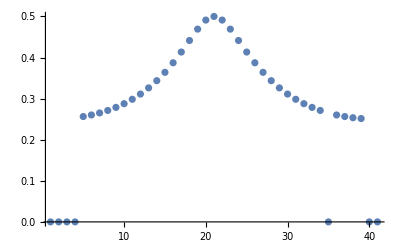

```mathematica
With[{data=Table[
Function[maximizationOutput,
QWEvolve[{1,0},Partition[#,2]&@maximizationOutput["CoinParameters"]⟦All,2⟧]//QWProjectionProbability@{1,1}
][
searchCoinParameters[3,Normalize@{1,1,1,ⅇ^(ⅈ α)},"IncludeProjectionInMaximization"->False,"PrintExecutionMessages"->False]
],
{α,0,2π,2π/40.}
]},
ListPlot[
data,
PlotRange->All
]
]
```

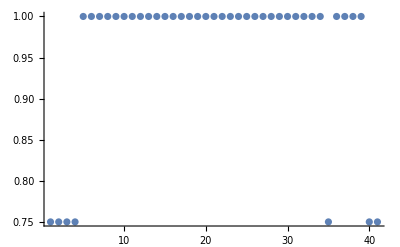

```mathematica
With[{data=Table[
searchCoinParameters[3,Normalize@{1,1,1,ⅇ^(ⅈ α)},"IncludeProjectionInMaximization"->False,"PrintExecutionMessages"->False]["FinalFidelity"],
{α,0,2π,2π/40.}
]},
ListPlot[
data,
PlotRange->All
]
]
```

```mathematica
Get[FileNameJoin@{NotebookDirectory[],"searchCoinParameters.m"}];
searchCoinParameters[2,"CacheFinalExpression"->False]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{searchCoinParameters`Private`θ[1]→0.523976,searchCoinParameters`Private`ξ[1]→1.03298,searchCoinParameters`Private`θ[2]→0.718013,searchCoinParameters`Private`ξ[2]→-1.37042,searchCoinParameters`Private`α→1.12391},TargetState→{-0.291641+0.241512 ⅈ,-0.227069-0.772387 ⅈ,-0.336536-0.308577 ⅈ}|>

```mathematica
resultToProjectionProbability[result_]:=QWEvolve[{1,0},Partition[#,2]&@result["CoinParameters"]⟦All,2⟧]//QWProjectionProbability@{1,1}
```

```mathematica
searchCoinParameters[4,Normalize@randomComplexNormal[5],"IncludeProjectionInMaximization"->False,"PrintExecutionMessages"->False]
resultToProjectionProbability@%
```

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.197342,ξ[1]→0.411517,θ[2]→-0.600584,ξ[2]→-0.269044,θ[3]→0.726818,ξ[3]→-0.365166,θ[4]→0.708009,ξ[4]→-0.812361},TargetState→{-0.516237+0.166286 ⅈ,0.294738+0.465217 ⅈ,0.242003+0.495605 ⅈ,0.227795-0.186308 ⅈ,-0.0611601+0.089549 ⅈ}|>

0.358515

```mathematica
searchCoinParameters[16]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.548399,ξ[1]→-1.60549,θ[2]→-0.32799,ξ[2]→0.82442,θ[3]→-0.559397,ξ[3]→-0.249807,θ[4]→0.170735,ξ[4]→-1.78282,θ[5]→-0.212279,ξ[5]→-0.26565,θ[6]→0.520152,ξ[6]→0.770685,θ[7]→-0.0898036,ξ[7]→-1.80286,θ[8]→-0.598958,ξ[8]→1.01529,θ[9]→-0.367818,ξ[9]→-0.943748,θ[10]→-0.544037,ξ[10]→-0.346591,θ[11]→0.28355,ξ[11]→1.249,θ[12]→0.196596,ξ[12]→-2.21237,θ[13]→0.0884568,ξ[13]→1.04096,θ[14]→0.40156,ξ[14]→1.44294,θ[15]→0.304103,ξ[15]→0.490536,θ[16]→-0.732568,ξ[16]→-1.13172,α→0.287311},TargetState→{-0.0774168+0.101679 ⅈ,-0.19186-0.309913 ⅈ,-0.305452-0.241714 ⅈ,-0.282115+0.258144 ⅈ,0.187544+0.0887374 ⅈ,-0.0634965+0.241294 ⅈ,0.0257516+0.0255446 ⅈ,-0.0438302+0.0522665 ⅈ,-0.0320538-0.144271 ⅈ,0.145288-0.0295 ⅈ,-0.0824504-0.120532 ⅈ,0.000745154+0.231325 ⅈ,0.308358+0.180276 ⅈ,0.0838724-0.108508 ⅈ,-0.318567+0.0354144 ⅈ,0.0480467+0.0612026 ⅈ,-0.260001+0.0119203 ⅈ}|>

```mathematica
searchCoinParameters[18]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.113646,ξ[1]→-1.12684,θ[2]→0.232767,ξ[2]→1.97495,θ[3]→0.136369,ξ[3]→-2.4821,θ[4]→-0.427588,ξ[4]→3.51222,θ[5]→0.502012,ξ[5]→-2.23244,θ[6]→0.160807,ξ[6]→0.247411,θ[7]→-0.475824,ξ[7]→2.82248,θ[8]→-0.0874949,ξ[8]→-1.16653,θ[9]→-0.439227,ξ[9]→-2.07452,θ[10]→0.964141,ξ[10]→3.19859,θ[11]→0.312325,ξ[11]→-1.01453,θ[12]→-0.500146,ξ[12]→-1.73032,θ[13]→0.273343,ξ[13]→1.43924,θ[14]→0.883295,ξ[14]→-2.55915,θ[15]→0.0511211,ξ[15]→2.39495,θ[16]→0.53244,ξ[16]→-4.2225,θ[17]→-0.492912,ξ[17]→6.2876,θ[18]→0.163891,ξ[18]→-4.52845,α→0.319297},TargetState→{-0.142108-0.186354 ⅈ,-0.0828464+0.167931 ⅈ,-0.072903+0.0925074 ⅈ,0.0915877+0.131127 ⅈ,0.176411-0.310163 ⅈ,-0.175018+0.368767 ⅈ,-0.202673-0.0870255 ⅈ,-0.212676+0.10307 ⅈ,-0.0616935-0.0700044 ⅈ,0.107343-0.0383104 ⅈ,-0.0995424+0.159586 ⅈ,0.0974586-0.0668138 ⅈ,-0.157557+0.0937719 ⅈ,0.0663314+0.444099 ⅈ,-0.188984-0.122751 ⅈ,0.0953867-0.214851 ⅈ,-0.17628-0.116672 ⅈ,-0.0684874+0.0641229 ⅈ,-0.0706436+0.0362134 ⅈ}|>

```mathematica
searchCoinParameters[19]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.389123,ξ[1]→2.62485,θ[2]→-0.142109,ξ[2]→-0.320269,θ[3]→-0.0771792,ξ[3]→-2.31096,θ[4]→-0.0901666,ξ[4]→0.401009,θ[5]→-0.146583,ξ[5]→0.865706,θ[6]→-0.227461,ξ[6]→-1.78075,θ[7]→-0.220477,ξ[7]→1.41383,θ[8]→-0.131009,ξ[8]→-1.7188,θ[9]→-0.390627,ξ[9]→-1.06634,θ[10]→0.805042,ξ[10]→3.58746,θ[11]→-0.0917951,ξ[11]→-2.02425,θ[12]→-0.239607,ξ[12]→-0.70142,θ[13]→0.0587003,ξ[13]→3.22778,θ[14]→-0.120406,ξ[14]→-4.98421,θ[15]→-0.0446196,ξ[15]→4.43531,θ[16]→0.247714,ξ[16]→-1.56283,θ[17]→0.326776,ξ[17]→0.942496,θ[18]→-0.418913,ξ[18]→-1.21273,θ[19]→-0.249062,ξ[19]→0.694083,α→-0.0921486},TargetState→{0.0845797+0.00184606 ⅈ,0.215023+0.10752 ⅈ,-0.228767-0.150652 ⅈ,-0.46937+0.194271 ⅈ,-0.139088+0.0880715 ⅈ,0.109255-0.103948 ⅈ,-0.0714009-0.199896 ⅈ,-0.0133229+0.0792844 ⅈ,0.0449405-0.0638268 ⅈ,-0.0616721-0.00634475 ⅈ,0.244809+0.435102 ⅈ,0.00238555-0.0758821 ⅈ,0.0208189-0.0306149 ⅈ,0.0273469+0.123265 ⅈ,-0.00161174-0.0970476 ⅈ,-0.0351658-0.0681872 ⅈ,0.120742-0.1546 ⅈ,-0.0507374+0.0921184 ⅈ,-0.0949382+0.0630903 ⅈ,0.00460154+0.374811 ⅈ}|>

```mathematica
searchCoinParameters[19]//AbsoluteTiming
```

Preparing state...

Starting maximization...

{17.0132,<|FinalFidelity→1.,CoinParameters→{θ[1]→0.634022,ξ[1]→3.45214,θ[2]→-0.411611,ξ[2]→-0.853793,θ[3]→-0.353461,ξ[3]→0.606971,θ[4]→0.653535,ξ[4]→-2.10997,θ[5]→0.208935,ξ[5]→0.710142,θ[6]→-0.382362,ξ[6]→1.08828,θ[7]→-0.160182,ξ[7]→0.347788,θ[8]→0.333308,ξ[8]→-1.44505,θ[9]→-0.283309,ξ[9]→1.57745,θ[10]→-0.0603926,ξ[10]→-2.61955,θ[11]→-0.623552,ξ[11]→-1.82707,θ[12]→0.0208418,ξ[12]→0.460501,θ[13]→0.323543,ξ[13]→2.17608,θ[14]→0.414068,ξ[14]→-0.991863,θ[15]→0.220162,ξ[15]→-0.685197,θ[16]→0.259022,ξ[16]→-0.0707604,θ[17]→0.471407,ξ[17]→3.13375,θ[18]→0.61416,ξ[18]→-2.52703,θ[19]→-0.147351,ξ[19]→1.6021,α→-0.512725},TargetState→{0.078793+0.171506 ⅈ,-0.0499455+0.128547 ⅈ,-0.114772+0.315436 ⅈ,0.155422+0.143577 ⅈ,-0.0421968-0.206983 ⅈ,-0.0342044+0.216584 ⅈ,-0.0394148-0.321175 ⅈ,0.0489696+0.0302937 ⅈ,-0.161575+0.0933658 ⅈ,0.263669-0.355781 ⅈ,0.0790485-0.231129 ⅈ,-0.0296718-0.196954 ⅈ,0.118875-0.0996238 ⅈ,0.191948+0.0725141 ⅈ,-0.138463+0.0547618 ⅈ,0.0891946+0.013418 ⅈ,0.195953+0.0413679 ⅈ,0.189155-0.0569184 ⅈ,-0.161577+0.0349822 ⅈ,0.0386334-0.22915 ⅈ}|>}

```mathematica
searchCoinParameters[19]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.879312,ξ[1]→-0.486134,θ[2]→-0.200577,ξ[2]→0.676995,θ[3]→-0.161979,ξ[3]→0.484546,θ[4]→-0.563197,ξ[4]→-0.0104582,θ[5]→0.265956,ξ[5]→0.0944432,θ[6]→0.26815,ξ[6]→0.253688,θ[7]→0.202788,ξ[7]→-0.652344,θ[8]→-0.694164,ξ[8]→-0.47791,θ[9]→-0.27709,ξ[9]→0.239733,θ[10]→0.0205322,ξ[10]→-0.760334,θ[11]→0.0735008,ξ[11]→-1.84398,θ[12]→-0.246785,ξ[12]→3.38556,θ[13]→0.533642,ξ[13]→-2.26742,θ[14]→-0.558401,ξ[14]→2.24527,θ[15]→-0.153483,ξ[15]→-0.814475,θ[16]→0.575795,ξ[16]→0.44226,θ[17]→0.771946,ξ[17]→0.693813,θ[18]→-0.462713,ξ[18]→0.343423,θ[19]→0.299738,ξ[19]→-0.611963,α→0.633356},TargetState→{-0.0499348-0.176962 ⅈ,0.00282451+0.0697927 ⅈ,0.0154358-0.0905819 ⅈ,-0.113515-0.396088 ⅈ,0.246969-0.103046 ⅈ,0.0497041-0.273779 ⅈ,0.0969721+0.0979089 ⅈ,0.144582+0.254866 ⅈ,-0.125203+0.0278645 ⅈ,0.0548062+0.22841 ⅈ,0.110981+0.0828225 ⅈ,-0.0559435-0.181087 ⅈ,-0.135893+0.25429 ⅈ,0.0693368-0.016569 ⅈ,0.132904+0.244274 ⅈ,-0.213125+0.130693 ⅈ,-0.0375462-0.223907 ⅈ,0.0393973-0.100805 ⅈ,-0.0616367-0.183654 ⅈ,-0.13272+0.236718 ⅈ}|>

```mathematica
searchCoinParameters[22]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-1.53308,ξ[1]→1.07755,θ[2]→0.274433,ξ[2]→-3.61175,θ[3]→-0.365929,ξ[3]→3.32387,θ[4]→-0.388033,ξ[4]→-0.213769,θ[5]→0.35957,ξ[5]→-0.395987,θ[6]→-0.400849,ξ[6]→0.190918,θ[7]→-0.345945,ξ[7]→-4.58646,θ[8]→-0.224549,ξ[8]→4.67026,θ[9]→0.714968,ξ[9]→-2.95312,θ[10]→-0.335599,ξ[10]→2.3408,θ[11]→0.574149,ξ[11]→-1.08057,θ[12]→-0.154701,ξ[12]→-1.4559,θ[13]→-0.164958,ξ[13]→1.82178,θ[14]→-0.31993,ξ[14]→-0.0407475,θ[15]→-0.49833,ξ[15]→-2.71022,θ[16]→0.579721,ξ[16]→2.76145,θ[17]→-0.228785,ξ[17]→0.656945,θ[18]→-0.258606,ξ[18]→-2.03814,θ[19]→0.646426,ξ[19]→0.625873,θ[20]→-0.241043,ξ[20]→0.24058,θ[21]→0.30575,ξ[21]→-1.57021,θ[22]→-0.217445,ξ[22]→-0.154587,α→-1.08543},TargetState→{-0.0194276+0.00580265 ⅈ,-0.12086-0.0582444 ⅈ,-0.0136564+0.0123361 ⅈ,0.101534-0.00672679 ⅈ,-0.0275473-0.155773 ⅈ,-0.193491-0.0050662 ⅈ,0.202528+0.0467882 ⅈ,-0.20569-0.282096 ⅈ,0.209385-0.103155 ⅈ,-0.191502+0.154342 ⅈ,0.149488+0.061889 ⅈ,0.160862-0.163186 ⅈ,-0.035835+0.0366376 ⅈ,0.0343749+0.239339 ⅈ,0.152045-0.0377801 ⅈ,0.0284754+0.0951359 ⅈ,-0.184034-0.32421 ⅈ,0.128818+0.193029 ⅈ,-0.087186+0.0905856 ⅈ,-0.24776-0.0876825 ⅈ,0.156216-0.142554 ⅈ,0.180466+0.23559 ⅈ,-0.200588-0.0583879 ⅈ}|>

## Analysis of results from maximization

#### Analysis utilities

```mathematica
getOnlyCoinParsWithoutProjection[pars_List]:=If[pars⟦-1,1⟧===α,Most@pars⟦All,2⟧,pars⟦All,2⟧];
projectionParameter[pars_List]:=If[pars⟦-1,1⟧===α,
{α,Sqrt[1-α^2]}/.Last@pars,
Normalize@{1,1}
];

computeWholeStateFromResult[result_Association]:=With[{
coinParameters=getOnlyCoinParsWithoutProjection@result["CoinParameters"]
},
QWEvolve[{1,0},Partition[#,2]&@coinParameters]
];

computeTargetFromResult[result_Association]:=With[{
targetState=result["TargetState"],
coinParameters=getOnlyCoinParsWithoutProjection@result["CoinParameters"]
},
Block[{evolutionMatrix,evolvedState,projection},
evolvedState=QWEvolve[{1,0},PadRight[#,3]&/@Partition[#,2]&@coinParameters];
projection=projectionParameter@result["CoinParameters"];
QWProjectCoin[evolvedState,projection]
]
];

computeFidelityFromResult[result_Association]:=With[{
targetState=result["TargetState"],
coinParameters=getOnlyCoinParsWithoutProjection@result["CoinParameters"]
},
Block[{evolutionMatrix,evolvedState,projection},
evolvedState=QWEvolve[{1,0},PadRight[#,3]&/@Partition[#,2]&@coinParameters];
projection=projectionParameter@result["CoinParameters"];
QFidelity[
QWProjectCoin[evolvedState,projection],
targetState
]
]
];

computeProbabilityFromResult[result_Association]:=With[{
targetState=result["TargetState"],
coinParameters=getOnlyCoinParsWithoutProjection@result["CoinParameters"]
},
Block[{evolutionMatrix,evolvedState,projection},
evolvedState=QWEvolve[{1,0},PadRight[#,3]&/@Partition[#,2]&@coinParameters];
projection=projectionParameter@result["CoinParameters"];

QWProjectionProbability[evolvedState,projection]
]
];
```

```mathematica
results
```

<|FinalFidelity→0.999999,CoinParameters→{θ[1]→-0.594915,ξ[1]→1.92305,θ[2]→-0.162149,ξ[2]→-1.31077,θ[3]→-0.809433,ξ[3]→2.68994,θ[4]→-0.0897499,ξ[4]→-0.839079,θ[5]→0.599533,ξ[5]→-1.50832,θ[6]→-0.046818,ξ[6]→1.81823,θ[7]→-0.29112,ξ[7]→-2.78985,θ[8]→-0.405098,ξ[8]→2.26923,θ[9]→0.252905,ξ[9]→-1.70443,θ[10]→0.419752,ξ[10]→0.505724,α→0.167478},TargetState→{0.115267+0. ⅈ,-0.285366+0.159916 ⅈ,0.0304173-0.0515962 ⅈ,-0.100062-0.0752707 ⅈ,-0.0111078-0.0763149 ⅈ,0.341837+0.515402 ⅈ,-0.0707687-0.0529947 ⅈ,-0.0042906-0.197701 ⅈ,0.292087+0.345025 ⅈ,0.0904939+0.0413051 ⅈ,0.451374-0.0842005 ⅈ}|>

#### 5 steps

```mathematica
data5stepsNMax=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*5steps*_corrected.mx"};
data5stepsNMax//Length;

(*data5stepsNMaxProbs=computeProbabilityFromResult/@data5stepsNMax//monitorMap;
exportHere["nmaximize_5steps_probabilities.mx",data5stepsNMaxProbs]*)
data5stepsNMaxProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_5steps_probabilities.mx"}];
```

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data5stepsNMax,Flatten@Position[data5stepsNMax⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data5stepsNMaxProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[0,14,.5],ControlType->Slider,Appearance->"Labeled"}
]
```

Stability of solutions:

```mathematica
searchCoinParameters[5,Normalize@ConstantArray[1,6],
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
```

Preparing state...

Starting maximization...

<|FinalFidelity→0.89129181919230449083,CoinParameters→{θ[1]→-0.20564683001429986212,ξ[1]→1.0661923441725643961,θ[2]→0.42664957617269139862,ξ[2]→2.077951626225338023,θ[3]→-0.0032185555254551303343,ξ[3]→0.53082493043289675889,θ[4]→-1.0927365660276712697,ξ[4]→0.0025059571971322021091,θ[5]→-2.3015907450699344534,ξ[5]→-0.0028309012375717766149},TargetState→{1/(√6),1/(√6),1/(√6),1/(√6),1/(√6),1/(√6)}|>

```mathematica
searchCoinParameters[5,Normalize@ConstantArray[1,6],
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//stabilityAnalysis`plotFidelityVsParameters[{0.9,1.1},"TypeOfPerturbation"->Times]
```

Preparing state...

Compiling function for caching...

Starting maximization...

-Graphics-

```mathematica
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//plotFidelityVsParameters[{0.9,1.1},"TypeOfPerturbation"->Times]
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//plotFidelityVsParameters[{-1,1.},"TypeOfPerturbation"->Plus]
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False
]//plotFidelityVsParameters@{0.9,1.1}
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
searchCoinParameters[5,
"IncludeProjectionInMaximization"->False
]//plotFidelityVsParameters@{0.9,1.1}
```

```mathematica
PrintDefinitions@plotFidelityVsParameters
```

8ing5_shm23FrontEndObject[LinkObject["8ing5_shm", 3, 1]]23Global`plotFidelityVsParameters

```mathematica
searchCoinParameters[5,
"IncludeProjectionInMaximization"->False
]//plotFidelityVsParameters@{0.9,1.1}
```

Preparing state...

Starting maximization...

-Graphics-

#### 19 steps

```mathematica
data19steps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*19steps*_corrected.mx"};
data19steps//Length;
```

```mathematica
(*data19stepsProbs=computeProbabilityFromResult/@data19steps//monitorMap;
exportHere["nmaximize_19steps_probabilities.mx",data19stepsProbs]*)
data19stepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_19steps_probabilities.mx"}];
```

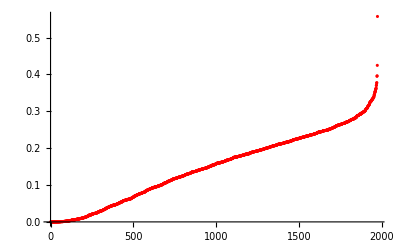

```mathematica
ListPlot[
Sort@data19stepsProbs,
PlotRange->All,PlotStyle->Red
]
```

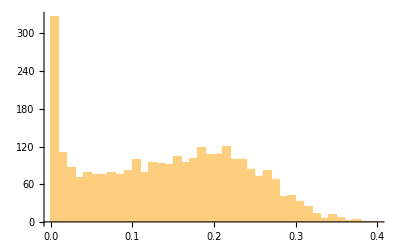

```mathematica
Histogram[data19stepsProbs,40]
```

On the other hand, let’s see what happens if we only consider the projection probabilities associated with the states obtained with good fidelities:

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data19steps,Flatten@Position[data19steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data19stepsProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[0,14,.5],ControlType->Slider,Appearance->"Labeled"}
]
```

#### 20 steps

```mathematica
data20steps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*20steps*_corrected.mx"};
```

```mathematica
computeTargetFromResult@First@data20steps
```

{-0.023324-0.313501 ⅈ,-0.00167684+0.0163723 ⅈ,0.0526861+0.187663 ⅈ,-0.0052893-0.0517087 ⅈ,-0.0696381-0.0699305 ⅈ,-0.151423+0.0710714 ⅈ,-0.243091+0.0928453 ⅈ,-0.124506+0.12365 ⅈ,0.0111806+0.0335208 ⅈ,-0.0492254-0.00381385 ⅈ,-0.128238+0.168903 ⅈ,0.160168-0.00750893 ⅈ,0.123975-0.166524 ⅈ,0.243231-0.0533927 ⅈ,-0.239693+0.139898 ⅈ,0.323715-0.0759767 ⅈ,-0.12786-0.272475 ⅈ,-0.0612236-0.149938 ⅈ,0.251398-0.0657417 ⅈ,-0.241732-0.184852 ⅈ,0.282608-0.00986604 ⅈ}

```mathematica
data20steps⟦1⟧["TargetState"]
```

{0.231453-0.212735 ⅈ,-0.0138826+0.00883889 ⅈ,-0.114531+0.157721 ⅈ,0.037281-0.03622 ⅈ,0.0116641-0.0979986 ⅈ,-0.149666-0.0747001 ⅈ,-0.2236-0.133102 ⅈ,-0.174216-0.0209757 ⅈ,-0.0193603+0.0295608 ⅈ,-0.0275389-0.040979 ⅈ,-0.212028+0.00416403 ⅈ,0.10523+0.120983 ⅈ,0.207518-0.00603266 ⅈ,0.19274+0.157682 ⅈ,-0.258402-0.101254 ⅈ,0.260373+0.206809 ⅈ,0.134435-0.269292 ⅈ,0.0796431-0.14102 ⅈ,0.207491+0.156429 ⅈ,-0.00492599-0.30427 ⅈ,0.183019+0.215568 ⅈ}

See all the obtained fidelities

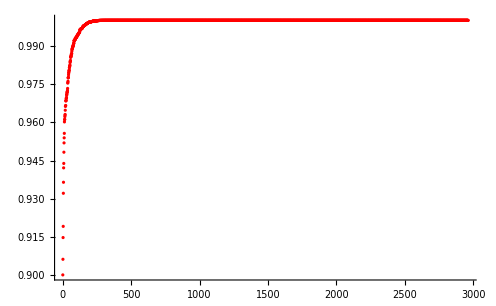

```mathematica
data20stepsSorted=SortBy[#["FinalFidelity"]&]@data20steps;
ListPlot[
data20stepsSorted⟦All,"FinalFidelity"⟧,
PlotRange->All,PlotStyle->Red
]
```

How do the projection probabilities behave?

```mathematica
data20stepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_20steps_probabilities.mx"}];
(*data20stepsProbs=computeProbabilityFromResult/@data20steps//monitorMap;*)
```

```mathematica
exportHere["nmaximize_20steps_probabilities.mx",data20stepsProbs]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\nmaximize_20steps_probabilities.mx

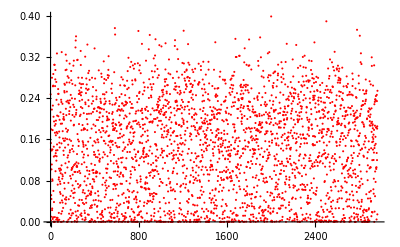

```mathematica
ListPlot[
data20stepsProbs,
PlotRange->All,PlotStyle->Red
]
```

Including all of the data we get something with an annoying peak around zero probability

```mathematica
Histogram[data20stepsProbs,40]
```

-Graphics-

On the other hand, let’s see what happens if we only consider the projection probabilities associated with the states obtained with good fidelities:

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data20steps,Flatten@Position[data20steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data20stepsProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[4,14,1],ControlType->Slider,Appearance->"Labeled"}
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

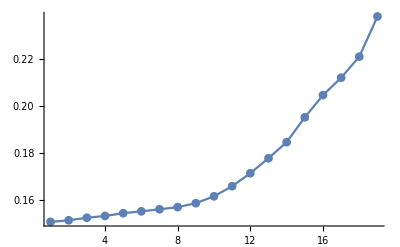

```mathematica
With[{data=Table[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data20steps,Flatten@Position[data20steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Mean@data20stepsProbs⟦onlyGoodFidelityIndices⟧
],
{threshold,4,13,.5}
]},
ListPlot[data,
PlotRange->All,Joined->True,PlotMarkers->Automatic
]
]
```

#### Visualization of projection probabilities of solutions obtained with NMaximize

```mathematica
ClearAll@probabilityHistograms2Thresholds;
Options@probabilityHistograms2Thresholds=Options@Histogram;
probabilityHistograms2Thresholds[nSteps_Integer,thresholds_List:{0,10},nBins_Integer:20,opts:OptionsPattern[]]:=Block[
{dataNSteps,dataNStepsProbs,goodIndices},
dataNSteps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*"<>ToString@nSteps<>"steps*_corrected.mx"};
dataNStepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_"<>ToString@nSteps<>"steps_probabilities.mx"}];

goodIndices[threshold_]:=Complement[Range@Length@dataNSteps,Flatten@Position[dataNSteps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]];

With[{data=Table[
dataNStepsProbs⟦goodIndices@threshold⟧,
{threshold,thresholds}
]},
Histogram[
data,nBins,"Count",
AxesStyle->texStyles["title"],
Evaluate@FilterRules[{opts},Options@Histogram]
]
]
];
```

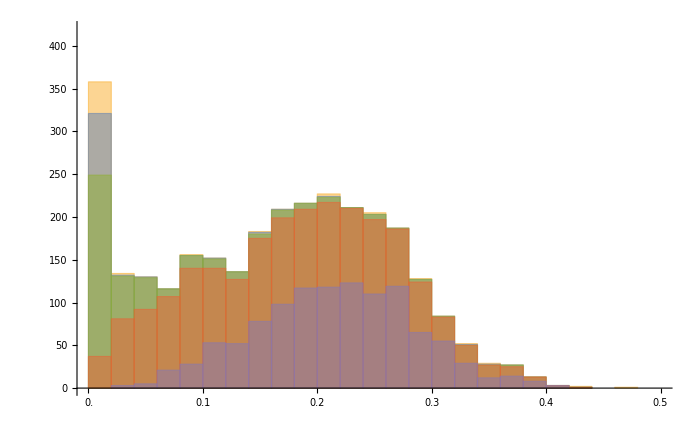

C:\Users\lk\Documents\docs\research\Quantum Walks (2016-2017)\code\probsHistogram_15steps_manyThresholds.pdf

```mathematica
fig2save=probabilityHistograms2Thresholds[15,{0,2,5,10,12},
PlotRange->{{0,.5},{0,420}},Ticks->{Range[0,.5,.05],Automatic},
ImageSize->700
]
exportHere["probsHistogram_15steps_manyThresholds.pdf",fig2save]
```

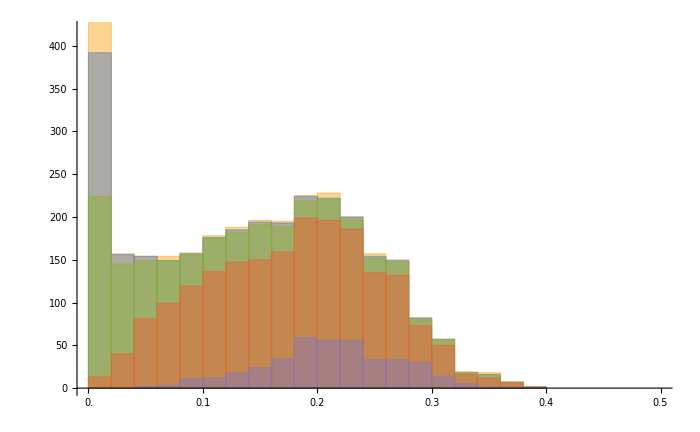

C:\Users\lk\Documents\docs\research\Quantum Walks (2016-2017)\code\probsHistogram_20steps_manyThresholds.pdf

```mathematica
fig2save=probabilityHistograms2Thresholds[20,{0,2,5,10,12},
PlotRange->{{0,.5},{0,420}},Ticks->{Range[0,.5,.05],Automatic},
ImageSize->700
]
exportHere["probsHistogram_20steps_manyThresholds.pdf",fig2save]
```

```mathematica
Manipulate[
probabilityHistograms2Thresholds[
nSteps,{0,firstThreshold,5,10,12},
PlotRange->{{0,.5},{0,450}},ImageSize->500
],
{{nSteps,20},4,20,1,Appearance->"Labeled"},
{{firstThreshold,2},0,14,1,Appearance->"Labeled"}
]
```